0.0625

3/16

3/16

1/8

2/3

1/16

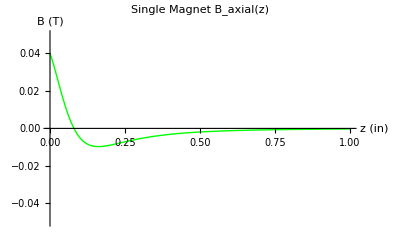

-Graphics3D-

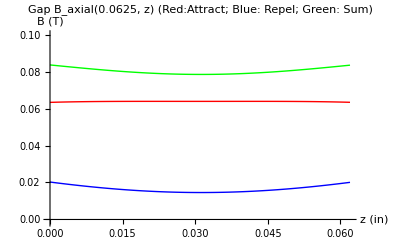

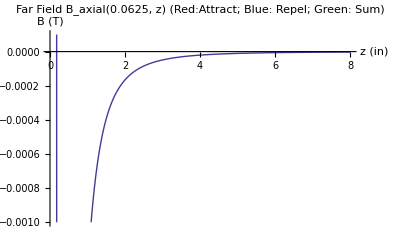

{0.,0.0835689}

{0.031,0.0784351}

-0.061433

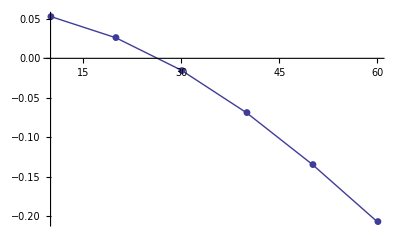

```mathematica
uZero=4*Pi* 10^(-7);
Iloop=10^3/1.3;
NCoils=3;
Rmag =3/16;
OppMagFaceDist=0;
RmagO=Rmag;
RmagRatio:=2/3 (*ID/OD ratio*)
RmagI:=RmagRatio*RmagO
MagThickness = 1/16;
zGapPA :=1 (*gap between two attracting magnets*)
zGapR:=1/32 (*z position, origin at left face of Right Attracting magnet*)
(*crossectional gap*)
(*crossectionGap :=1/8 -3/64*)
(*crossectionGap =0.0625*1.65;*)
crossectionGap =0.0625
sliceGap=0.07; (*3D slice Gap size*)
OppWeight:= Function[{OMFD,seg, mTh, mType},
(*linear weight*)
(* mType: "A", attractive; "R", repulsive*)
(*Notes: 
Meassured Belly => -0.06; ~800 G at (z = 0, Gap = 0.0625)

return 1-1.5w (on both) => -.14 belly; strength reduced to 0.1 at (0,0.0625)
2.5 (with +1/2 correction) => -0.06, .2 

no weight on AP (1000), return 1 - 1.5w => flat (-.003); strength 0.5 at (0,0.0625)
2.5 => -0.06, 0.5; corrected 1/2 | 
3 => -0.09, 0.5 ; corrected +1/2 to -1/2 | => +0.13, 0.55
5 (with +1/2 correction) => -0.03, 0.6
6 (,,) => -0.05, 0.6
7 (,,) => -0.07, 0.6 
8 (,,) => -0.08, 0.6

no weight on AP and RP, return n/a => peak (+.09); strength 0.5 at (0,0.0625)

1-3w on RP, 1-0.5w on AP => -0.13, 0.4
1-3w on RP, 0.5w on AP => -0.16, 0.2
*********>>>>>>>>>>1-9w on RP, 1+1.4w on AP => -0.06, 0.8
*)
w=(OMFD+(mTh/NCoils)*((NCoils-seg)-1/2))/(OMFD+mTh); (*ratio distance for Opposing magnet / far face distance*)
(*Print["In OppWeight"];
Print[w];*)
If[OMFD!=1000,If[mType=="R",1-9w,1+1.4w],1]
]
BzNCoil:=Function[{Radius, Current, zP,OMFDi},
BzC=(uZero*Current/2)*((Radius*2.54/100)^2 /((zP*2.54/100)^2+(Radius*2.54/100)^2)^1.5);
(*Print["In BzNCoil:"];
Print[zP];*)
BzC
]
BzMagnet:=Function[{ORadius, IRadius,zPos, Thickness, OMFDist,MagType},
(*zPos: magnet face closer to Gap*)
(*OMFDist: distance of Opposing Magnetization magnet*)
Current = Iloop/NCoils;
Bz=0; (*accumulator reset*)
n=1;
While[n<=NCoils,
(*Print["In loop: "];
Print[n];*)
Bz=Bz+OppWeight[OMFDist,n,Thickness, MagType]*(BzNCoil[IRadius, Current, zPos+(Thickness/NCoils)*(n-1/2), OMFDist]-
BzNCoil[ORadius, Current, zPos+(Thickness/NCoils)*(n-1/2), OMFDist]);
n=n+1
];
(*Print["After loop"];
Print[Bz];*)
Bz
]
(*===== Single =====*)
Bz1:=BzMagnet[RmagO, RmagI,zGapR,MagThickness,1000, "A"]
zGapPA=0;
data1=Table[{zGapR,Bz1},{zGapR,0,1,0.01}]//N; (*sweep z*)
(*==== Attracting Pair ====, made unweighted *)
zGapLA:=zGapPA-zGapR
Bz2RA:=BzMagnet[RmagO, RmagI,zGapR, MagThickness,0, "A"]
Bz2LA:=BzMagnet[RmagO, RmagI,zGapLA, MagThickness,0, "A"]
Bz2PA:=Bz2LA+Bz2RA
data2p=Table[{zGapPA,zGapR,Bz2PA},{zGapPA,0,0.2,.01},{zGapR,0,zGapPA,0.01}]//N; (*sweep Gap and z*)
data2pf=Flatten[data2p,1];
zGapPA :=crossectionGap
data2pgap=Table[{zGapR,Bz2PA},{zGapR,0,crossectionGap,0.001}]//N; (*sweep only z for crossection*)
data2pgapCase = Cases[data2pf,{sliceGap,y_,z_}->{y,z}];
ListPlot3D[data2pf,PlotRange->{-.2,0.45}];
Rmag
RmagO
RmagI
RmagRatio
MagThickness
(*==== Repelling Pair ====*)
zGapRR:=zGapR+MagThickness
zGapLR:=zGapPA-zGapR+MagThickness
Bz2RR:=-BzMagnet[RmagO, RmagI,zGapRR, MagThickness, 0, "R"]
Bz2LR:=-BzMagnet[RmagO, RmagI,zGapLR, MagThickness,0, "R"]
Bz2PR:=Bz2LR+Bz2RR
data2pr=Table[{zGapPA,zGapR,Bz2PR},{zGapPA,0,0.2,.01},{zGapR,0,zGapPA,0.01}]//N;
data2prf=Flatten[data2pr,1];
zGapPA :=crossectionGap
data2prgap=Table[{zGapR,Bz2PR},{zGapR,0,crossectionGap,0.001}]//N;
data2prgapCase = Cases[data2prf,{sliceGap,y_,z_}->{y,z}];
ListPlot3D[data2prf,PlotRange->{-.6,0.45}];
(*==== Assembly ====*)
Bz4 := Bz2PA+Bz2PR
data4=Table[{zGapPA,zGapR,Bz4},{zGapPA,.01,0.2,.01},{zGapR,0,zGapPA,0.01}]//N;
data4f=Flatten[data4,1];
zGapPA :=crossectionGap
data4gap=Table[{zGapR,Bz4},{zGapR,0,crossectionGap,0.001}]//N;
data4gapFar=Table[{zGapR,Bz4},{zGapR,0,8,0.01}]//N;
data4gapCase = Cases[data4f,{sliceGap,y_,z_}->{y,z}];
data4gapCase;
(*==== Plots ====*)
ListPlot[data1,Joined->True,PlotRange->{-0.05,0.05},PlotStyle->{Red,Blue,Green},AxesLabel->{"z (in)", "B (T)"}, PlotLabel->"Single Magnet B_axial(z)"] (*single magnet*)
ListPlot3D[data4f,PlotRange->{0.0294348,0.0294350}];
ListPlot3D[{data2pf,data2prf,data4f}, PlotStyle->{Red,Blue,Green}, PlotLabel->"Gap B_axial(gap width, z) (Red:Attract; Blue: Repel; Green: Sum)", AxesLabel->{"Attracting Gap (in)", "z (in)", "B (T)"}] (*Gap and z sweep plot*)
data2pf;
data2prf;
data4f;
data1;
ListPlot[{data2pgap,data2prgap,data4gap},Joined->True,PlotRange->{-.0015,0.1},PlotStyle->{Red,Blue,Green},AxesLabel->{"z (in)", "B (T)"}, PlotLabel->"Gap B_axial("<>ToString[crossectionGap]<>", z) (Red:Attract; Blue: Repel; Green: Sum)"] (*Crossection plot*)
ListPlot[{data2pgapCase,data2prgapCase,data4gapCase},Joined->True,PlotRange->{-.15,0.35},PlotStyle->{Red,Blue,Green},AxesLabel->{"z (in)", "B (arbitrary units)"}, PlotLabel->"B_axial(0.125) (Red:Attract; Blue: Repel; Green: Sum)"] (*Case slice plot*);
ListPlot[data4gapFar,Joined->True,PlotRange->{-.001,0.0001},AxesLabel->{"z (in)", "B (T)"},PlotLabel->"Far Field B_axial("<>ToString[crossectionGap]<>", z) (Red:Attract; Blue: Repel; Green: Sum)"] (*Far Field plot*)
data2pgap;
data2prgap;
data4gap;
(*==== Belly Calculation ====*)
Bface=data4gap[[1]]
Bcenter=data4gap[[Ceiling[Length[data4gap]/2]]]
(Bcenter[[2]]-Bface[[2]])/Bface[[2]]
ListPlot[{{10,0.053},{20,0.026},{30,-0.015},{40,-0.069},{50,-0.134},{60,-0.207}}, Joined->True, PlotMarkers->Automatic]
```